```mathematica
α[t_] := (I/(4*H[t]))*D[θ[t],t];
H[t_]:=Sqrt[1+t^2];
θ[t_]:=ArcCos[t/Sqrt[1+t^2]];
w[t_]:=Integrate[2*H[t],{t,0,t}];
wc=(-I*Pi)/2;
$Assumptions=Element[{t},Reals];
αs={0};
βs={1};

Do[
If[i==1,AppendTo[αs,α[t]]];

(*α[t_]=(-I^(i+1)*Factorial[i-1])/(2*Pi)*(1/(w[t]-wc)^i-1/(w[t]-Conjugate[wc])^i);*)
β[t_]:=(1/2)*Integrate[D[θ[t],t]*α[t],{t,-Infinity,t}];α[t_]=(I/2*H[t])*(D[α[t],t]+(1/4)*D[θ[t],t]*Integrate[D[θ[t],t]*α[t],{t,-Infinity,t}]);
AppendTo[αs,α[t]];
AppendTo[βs,β[t]],
{i,5}]
```

KernelConfiguration

```mathematica
Information[KernelConfiguration]
```

{1,1/768 (-8-35/((1+t^2)^2)+4/(1+t^2)-(8 t)/(√(1+t^2)))}

```mathematica
bbs[t]//Simplify
```

{{1/(√(1+t^2) (1.+t^2)^4)(0.00189757 ((1.-39.7614 ⅈ)+(4.-119.284 ⅈ) t^2+(6.-119.284 ⅈ) t^4+(4.-39.7614 ⅈ) t^6+1. t^8-(16.5+3.57103×10^-18 ⅈ) t √(1+t^2)-(32.-3.57103×10^-18 ⅈ) t^3 √(1+t^2)-14.5 t^5 √(1+t^2)+1. t^7 √(1+t^2)) Cos[1/2 ArcCos[t/(√(1+t^2))]]+((-0.00314375+0.0072493 ⅈ) t-(0.012575-0.0158032 ⅈ) t^3-(0.0188625-0.0104514 ⅈ) t^5-(0.012575-0.00249056 ⅈ) t^7-(0.00314375-0.00059299 ⅈ) t^9+(0.984674+0.000415093 ⅈ) √(1+t^2)+(3.96463+0.00183827 ⅈ) t^2 √(1+t^2)+(5.9721+0.00302425 ⅈ) t^4 √(1+t^2)+(3.989+0.00219406 ⅈ) t^6 √(1+t^2)+(0.996856+0.00059299 ⅈ) t^8 √(1+t^2)) Sin[1/2 ArcCos[t/(√(1+t^2))]])},{1/((1.+t^2)^4)(((-0.984674-0.000415093 ⅈ)-(3.96463+0.00183827 ⅈ) t^2-(5.9721+0.00302425 ⅈ) t^4-(3.989+0.00219406 ⅈ) t^6-(0.996856+0.00059299 ⅈ) t^8+((0.00314375-0.0072493 ⅈ) t)/(√(1+t^2))+((0.012575-0.0158032 ⅈ) t^3)/(√(1+t^2))+((0.0188625-0.0104514 ⅈ) t^5)/(√(1+t^2))+((0.012575-0.00249056 ⅈ) t^7)/(√(1+t^2))+((0.00314375-0.00059299 ⅈ) t^9)/(√(1+t^2))) Cos[1/2 ArcCos[t/(√(1+t^2))]]+1/(√(1+t^2))((0.00189757-0.07545 ⅈ)+(0.00759027-0.22635 ⅈ) t^2+(0.0113854-0.22635 ⅈ) t^4+(0.00759027-0.07545 ⅈ) t^6+(0.00189757+4.56823×10^-38 ⅈ) t^8-(0.0313099+6.77626×10^-21 ⅈ) t √(1+t^2)-(0.0607222-6.77626×10^-21 ⅈ) t^3 √(1+t^2)-0.0275147 t^5 √(1+t^2)+0.00189757 t^7 √(1+t^2)) Sin[1/2 ArcCos[t/(√(1+t^2))]])}}

```mathematica
Clear[t];
Clear[uminus];
n =4;
ϵ = 0.3018;
(*uplus[t_]:=Cos[θ[t]/2],Sin[θ[t]/2];
uminus[t_]:=Sin[θ[t]/2],-Cos[θ[t]/2];*)
uplus[t_]:={{Cos[θ[t]/2]},{Sin[θ[t]/2]}};
uminus[t_]:={{Sin[θ[t]/2]},{-Cos[θ[t]/2]}};
bb[n_,nt_]:=(ϵ^(n))*(((αs[[n+1]]/. t->nt)*uplus[nt])+( (βs[[n+1]]/. t->nt)*uminus[nt]));
bbs[nt_]:=Sum[bb[n,nt],{n,0,2}];
Qs = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]}}],{nt,-40+0.0001,40.0001,0.01}];
Rs = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{0,1},{1,0}}.bbs[ϵ*nt]}}],{nt,-40+0.0001,40.0001,0.01}];
Ss = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{1,0},{0,-1}}.bbs[ϵ*nt]}}],{nt,-40+0.0001,40.0001,0.01}];
XYs = Table[Flatten[{{ConjugateTranspose[bbs[ϵ*nt]].{{0,1},{1,0}}.bbs[ϵ*nt]},{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]}}],{nt,-40+0.0001,40.0001,0.01}];
```

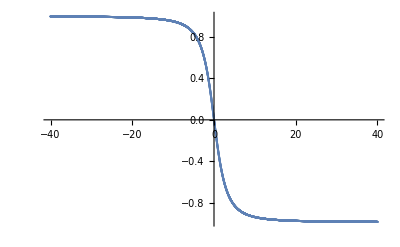

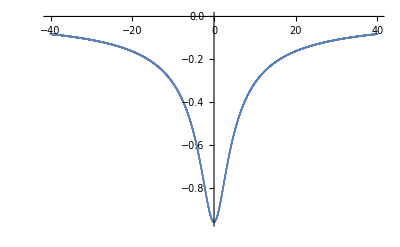

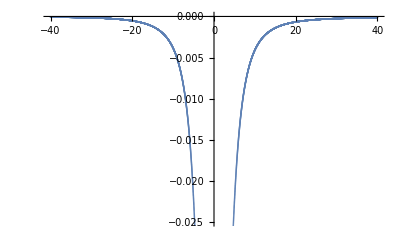

```mathematica
ListPlot[Ss]
ListPlot[Rs]
ListPlot[Qs]
```

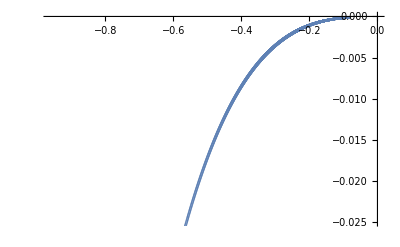

```mathematica
ListPlot[XYs]
```

```mathematica
p4 =ParametricPlot3D[Flatten[{ConjugateTranspose[bbs[u]].{{0,1},{1,0}}.bbs[u],ConjugateTranspose[bbs[u]].{{0,-I},{I,0}}.bbs[u],ConjugateTranspose[bbs[u]].{{1,0},{0,-1}}.bbs[u]}],{u,-2,2},PlotRange->{{-1,1},{-1,1},{-1,1}}];
p5 = Graphics3D[Sphere[{0,0,0}],PlotRange->{{-1,1},{-1,1},{-1,1}}];
Show[p4,p5]
```

-Graphics3D-

```mathematica
σ[t_]:=Integrate[2*Sqrt[1+(ϵ*dt)^2],{dt,0,t}]/Sqrt[2*ϵ*(Pi/2)];
σs =Table[σ[t],{t,-4+0.0001,4.0001,0.1}]
```

{-9.91214,-9.59255,-9.27768,-8.96748,-8.6619,-8.36087,-8.06435,-7.77227,-7.48457,-7.20117,-6.922,-6.64699,-6.37607,-6.10915,-5.84614,-5.58696,-5.33151,-5.0797,-4.83142,-4.58657,-4.34504,-4.10671,-3.87146,-3.63918,-3.40972,-3.18295,-2.95875,-2.73695,-2.51742,-2.3,-2.08453,-1.87085,-1.6588,-1.4482,-1.23888,-1.03066,-0.823375,-0.616828,-0.410839,-0.205223,0.000205398,0.205634,0.41125,0.61724,0.823789,1.03108,1.2393,1.44862,1.65922,1.87128,2.08496,2.30043,2.51786,2.73739,2.95919,3.1834,3.41017,3.63964,3.87193,4.10718,4.34552,4.58706,4.83191,5.0802,5.33202,5.58747,5.84666,6.10968,6.37661,6.64754,6.92255,7.20173,7.48514,7.77285,8.06494,8.36147,8.6625,8.96809,9.2783,9.59318,9.91279}

```mathematica
XYZs = Table[Flatten[{{ConjugateTranspose[bbs[ϵ*nt]].{{0,1},{1,0}}.bbs[ϵ*nt]},{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]},
{ConjugateTranspose[bbs[ϵ*nt]].{{1,0},{0,-1}}.bbs[ϵ*nt]}
}],{nt,-50,50,0.05}];
```

```mathematica
SdotE=(#.Table[PauliMatrix[k],{k,3}]&/@XYZs);
```

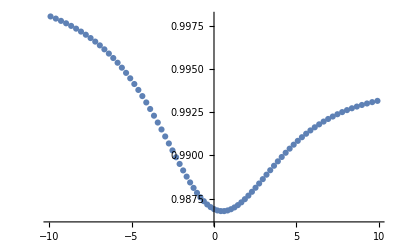

```mathematica
ntRange=Range[-4+0.0001,4.0001,0.1];
results=MapThread[Function[{nt,SdotEValue,sig},Flatten[{sig,Sqrt[(1+ConjugateTranspose[bbs[ϵ*nt]].SdotEValue.bbs[ϵ*nt])/2]}]],{ntRange,SdotE,σs}];
yValue=1-0.0055;
(*points=Table[{x,yValue},{x,-10,10,0.1}];
p1= ListLinePlot[points,PlotRange->{{-4,4},{yValue-0.01,yValue+0.01}}];*)
p2 = ListPlot[results//Chop];
Show[p2]
```

```mathematica
Re[XYZs]
```

{{-0.0661083,-0.0000347371,0.997812},{-0.0661742,-0.0000348411,0.997808},1997,{-0.0658301,-0.0000915978,-0.985154},{-0.0657646,-0.000091438,-0.985158}}
 |  |  |  |

```mathematica
Qs = Table[Flatten[{nt,{ConjugateTranspose[bbs[ϵ*nt]].{{0,-I},{I,0}}.bbs[ϵ*nt]}}],{nt,-2+0.0001,2.0001,0.001}];
```

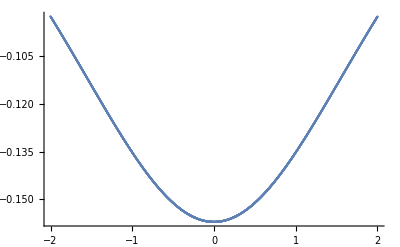

```mathematica
ListPlot[Qs]
```

```mathematica
$VersionNumber
```

12.3